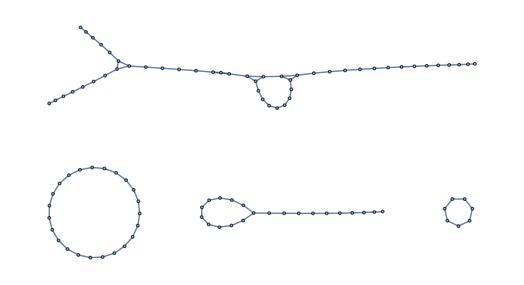

```mathematica
data=ReadList["F:\\Trabajos\\Estudio\\Fisica\\Escuela\\IB\\Semestre 5\\Tesis\\Net_Generation\\Test03.txt",{Number,Number,Number}];posic=Position[data, {0,0,0}]; t=Table[data[[i,1]]<->data[[i,2]], {i, 1, posic[[1,1]]-1}];cc=ConnectedComponents[Graph[t]]; Graph[t]
```

```mathematica
x=Evaluate[n-Total[Table[Length[cc[[i]]], {i, 1, Length[cc]}]]]
```

-10+n

```mathematica
ncc=Length[cc]; Do[{ncc=ncc+1}, x]; ncc
```

Do::nliter: Non-list iterator x at position 2 does not evaluate to a real numeric value.

1

```mathematica
t=Table[data[[i,1]]<->data[[i,2]], {i, 1, posic[[1,1]]}];
```

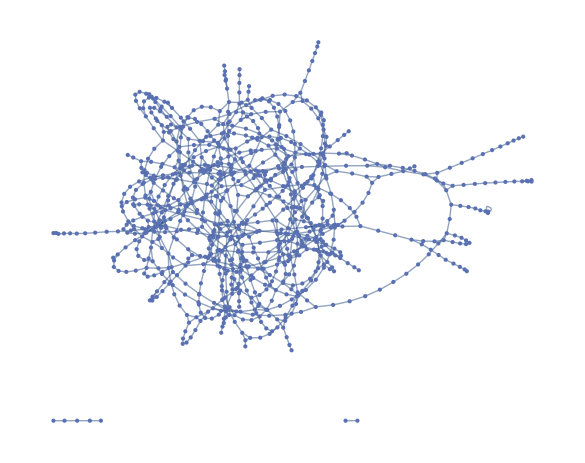

```mathematica
Graph[t]
```

```mathematica
VertexCount[%2]
```

1000

```mathematica
Length[ConnectedComponents[Graph[t]]]
```

3

```mathematica
EdgeCount[%2]
```

1186

```mathematica
VertexCount[%2]
```

1000

```mathematica
VertexCount[%2]
```

20

```mathematica
EdgeCount[%2]
```

25

```mathematica
VertexCount[%5]
```

VertexCount::graph: A graph object is expected at position 1 in VertexCount[%5].

VertexCount[%5]

```mathematica
cc=ConnectedComponents[Graph[t]]
```

{{0,2,5,1,13,19,3,10,11,4,7,6,18,8,9,14,12,15,16,17}}

```mathematica
LocalClusteringCoefficient[Graph[t]]
```

{1/3,1/3,1/3,1/3,0,1/10,0,0,0,0}

```mathematica
n-Total[Table[Length[cc[[i]]], {i, 1, Length[cc]}]]
```

{44}

```mathematica
DegreeGraphDistribution[Graph[t]];
```

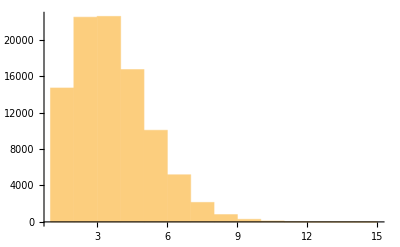

```mathematica
Histogram[VertexDegree[Graph[t]]]
```

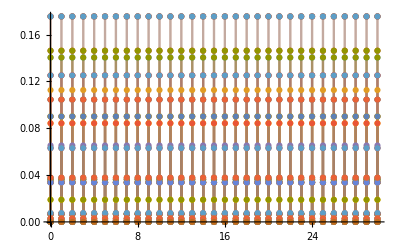

```mathematica
DiscretePlot[Table[PDF[PoissonDistribution[λ],k],{λ,{5,10,20}}]//Evaluate,{k,0,30}]
```

```mathematica
PDF[PoissonDistribution[λ],k];
```

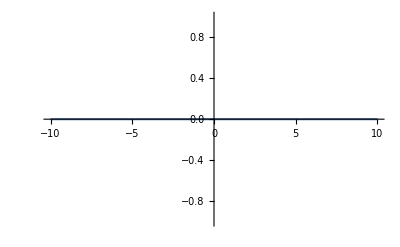

```mathematica
Plot[PDF[PoissonDistribution[3], x], {x, -10,10}, Filling->Axis]
```

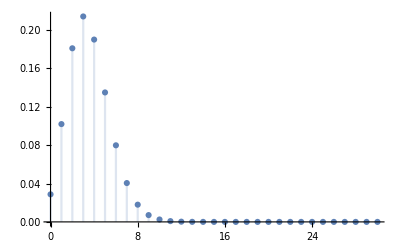

```mathematica
DiscretePlot[Table[PDF[PoissonDistribution[λ],k], {λ, {3.55}}]//Evaluate, {k, 0, 30}, PlotRange->All, PlotMarkers->Automatic]
```

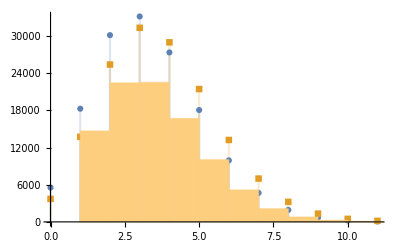

```mathematica
Show[DiscretePlot[Table[PDF[PoissonDistribution[λ],k]*(posic[[1,1]]-1), {λ, {3.3, 3.7}}]//Evaluate, {k, 0, 11}, PlotRange->Automatic, PlotMarkers->Automatic], Histogram[VertexDegree[Graph[t]]]]
```